```mathematica
SetDirectory["/home/atanu/Dropbox/Mathematica"]
```

/home/atanu/Dropbox/Mathematica

```mathematica
<<twoloop.m
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

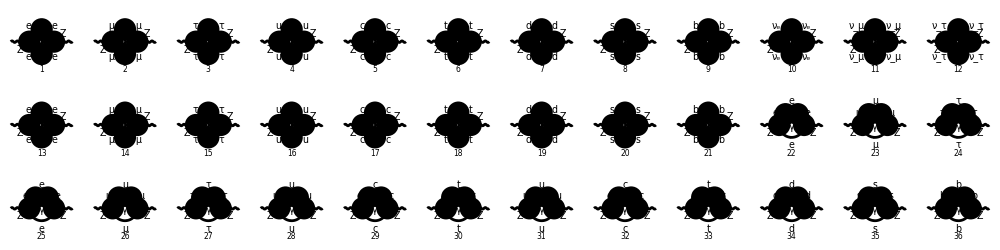

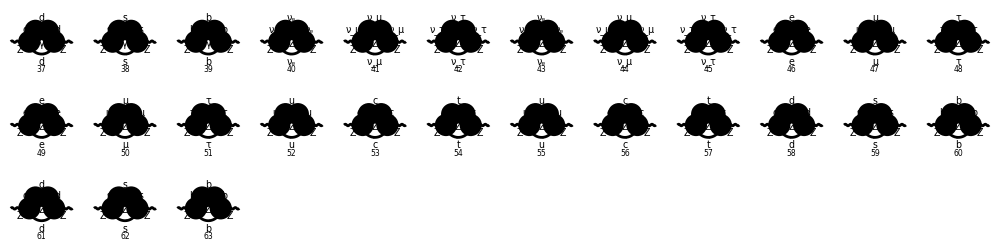

```mathematica
process = {V[2]}->{V[2]};
ins = InsertFields[TopologyList[topslist[[4]], topslist[[5]]], process, ExcludeParticles ->{U,S, V[3]}];
(*;  U,S,V[1],V[3],F[1],F[2,{2}],F[2,{3}],F[3],F[4]*)
Paint[ins,  ColumnsXRows -> {12,3}, ImageSize -> {1000, 250}];
```

CalcTwoLoopAmp[Ins,  No. of Diagrams]:

```mathematica
CalcTwoLoopAmp[ins,63]
```

FCFAConvert::sumOverWarn: You are omitting SumOver objects that may represent a nontrivial summation. This may lead to a loss of overall factors multiplying some of your diagrams. Please make sure that this is really what you want.

General::stop: Further output of FCFAConvert::sumOverWarn will be suppressed during this calculation.

Done

```mathematica
DeleteDuplicates[amplist]
```

{I00000}

```mathematica
intlist
```

(I00000 | 24
Itt0tt | 3
I00z00 | 33
Ittztt | 3)

```mathematica
Do[Print[ Feynints[intlist[[i]][[1]]]],{i,Length[intlist]}]
```

{I00000(-1,-1,1,2,1),I00000(-1,0,0,2,1),I00000(-1,0,1,1,1),I00000(-1,0,1,2,0),I00000(-1,0,1,2,1),I00000(-1,1,1,1,0),I00000(-1,1,1,1,1),I00000(0,-1,1,1,1),I00000(0,-1,1,2,1),I00000(0,0,0,1,1),I00000(0,0,0,2,1),I00000(0,0,1,0,1),I00000(0,0,1,1,0),I00000(0,0,1,1,1),I00000(0,0,1,2,0),I00000(0,0,1,2,1),I00000(0,1,0,1,0),I00000(0,1,0,1,1),I00000(0,1,1,0,0),I00000(0,1,1,0,1),I00000(0,1,1,1,-1),I00000(0,1,1,1,0),I00000(0,1,1,1,1),I00000(1,-1,1,1,1),I00000(1,-1,1,2,1),I00000(1,0,0,2,1),I00000(1,0,1,-1,1),I00000(1,0,1,0,0),I00000(1,0,1,0,1),I00000(1,0,1,1,0),I00000(1,0,1,1,1),I00000(1,0,1,2,0),I00000(1,0,1,2,1),I00000(1,1,-1,1,1),I00000(1,1,0,0,0),I00000(1,1,0,0,1),I00000(1,1,0,1,0),I00000(1,1,0,1,1),I00000(1,1,1,0,0),I00000(1,1,1,0,1),I00000(1,1,1,1,0),I00000(1,1,1,1,1)}

{Itt0tt(-1,-1,1,2,1),Itt0tt(-1,0,0,2,1),Itt0tt(-1,0,1,1,1),Itt0tt(-1,0,1,2,0),Itt0tt(-1,0,1,2,1),Itt0tt(-1,1,1,1,0),Itt0tt(-1,1,1,1,1),Itt0tt(0,-1,1,1,1),Itt0tt(0,-1,1,2,1),Itt0tt(0,0,0,1,1),Itt0tt(0,0,0,2,1),Itt0tt(0,0,1,0,1),Itt0tt(0,0,1,1,0),Itt0tt(0,0,1,1,1),Itt0tt(0,0,1,2,0),Itt0tt(0,0,1,2,1),Itt0tt(0,1,0,1,0),Itt0tt(0,1,0,1,1),Itt0tt(0,1,1,0,0),Itt0tt(0,1,1,0,1),Itt0tt(0,1,1,1,-1),Itt0tt(0,1,1,1,0),Itt0tt(0,1,1,1,1),Itt0tt(1,-1,1,1,1),Itt0tt(1,-1,1,2,1),Itt0tt(1,0,0,2,1),Itt0tt(1,0,1,-1,1),Itt0tt(1,0,1,0,0),Itt0tt(1,0,1,0,1),Itt0tt(1,0,1,1,0),Itt0tt(1,0,1,1,1),Itt0tt(1,0,1,2,0),Itt0tt(1,0,1,2,1),Itt0tt(1,1,-1,1,1),Itt0tt(1,1,0,0,0),Itt0tt(1,1,0,0,1),Itt0tt(1,1,0,1,0),Itt0tt(1,1,0,1,1),Itt0tt(1,1,1,0,0),Itt0tt(1,1,1,0,1),Itt0tt(1,1,1,1,0),Itt0tt(1,1,1,1,1)}

{I00z00(-1,-1,1,2,1),I00z00(-1,0,0,2,1),I00z00(-1,0,1,1,1),I00z00(-1,0,1,2,0),I00z00(-1,0,1,2,1),I00z00(-1,1,1,1,0),I00z00(-1,1,1,1,1),I00z00(0,-1,1,1,1),I00z00(0,-1,1,2,1),I00z00(0,0,0,1,1),I00z00(0,0,0,2,1),I00z00(0,0,1,0,1),I00z00(0,0,1,1,0),I00z00(0,0,1,1,1),I00z00(0,0,1,2,0),I00z00(0,0,1,2,1),I00z00(0,1,0,1,0),I00z00(0,1,0,1,1),I00z00(0,1,1,0,0),I00z00(0,1,1,0,1),I00z00(0,1,1,1,-1),I00z00(0,1,1,1,0),I00z00(0,1,1,1,1),I00z00(1,-1,1,1,1),I00z00(1,-1,1,2,1),I00z00(1,0,0,2,1),I00z00(1,0,1,-1,1),I00z00(1,0,1,0,0),I00z00(1,0,1,0,1),I00z00(1,0,1,1,0),I00z00(1,0,1,1,1),I00z00(1,0,1,2,0),I00z00(1,0,1,2,1),I00z00(1,1,-1,1,1),I00z00(1,1,0,0,0),I00z00(1,1,0,0,1),I00z00(1,1,0,1,0),I00z00(1,1,0,1,1),I00z00(1,1,1,0,0),I00z00(1,1,1,0,1),I00z00(1,1,1,1,0),I00z00(1,1,1,1,1)}

{Ittztt(-1,-1,1,2,1),Ittztt(-1,0,0,2,1),Ittztt(-1,0,1,1,1),Ittztt(-1,0,1,2,0),Ittztt(-1,0,1,2,1),Ittztt(-1,1,1,1,0),Ittztt(-1,1,1,1,1),Ittztt(0,-1,1,1,1),Ittztt(0,-1,1,2,1),Ittztt(0,0,0,1,1),Ittztt(0,0,0,2,1),Ittztt(0,0,1,0,1),Ittztt(0,0,1,1,0),Ittztt(0,0,1,1,1),Ittztt(0,0,1,2,0),Ittztt(0,0,1,2,1),Ittztt(0,1,0,1,0),Ittztt(0,1,0,1,1),Ittztt(0,1,1,0,0),Ittztt(0,1,1,0,1),Ittztt(0,1,1,1,-1),Ittztt(0,1,1,1,0),Ittztt(0,1,1,1,1),Ittztt(1,-1,1,1,1),Ittztt(1,-1,1,2,1),Ittztt(1,0,0,2,1),Ittztt(1,0,1,-1,1),Ittztt(1,0,1,0,0),Ittztt(1,0,1,0,1),Ittztt(1,0,1,1,0),Ittztt(1,0,1,1,1),Ittztt(1,0,1,2,0),Ittztt(1,0,1,2,1),Ittztt(1,1,-1,1,1),Ittztt(1,1,0,0,0),Ittztt(1,1,0,0,1),Ittztt(1,1,0,1,0),Ittztt(1,1,0,1,1),Ittztt(1,1,1,0,0),Ittztt(1,1,1,0,1),Ittztt(1,1,1,1,0),Ittztt(1,1,1,1,1)}

```mathematica
<<substitution4.m
```

To see the amplitudes:

```mathematica
feyn = F00000/.D->d;
st1 = feyn/.IRule//Simplify;
st2= st1/.{ mt^2->"\mt2", mZ^2 -> "\mz2", mZ^4 -> "\mz4",  mZ^6 -> "\mz6",  mW^2->"\mw2", mH^2->"\mh2", sw^2->"\sw2",sw^4->"\sw4",cw^2->"\cw2",cw^4->"\cw4", cw^6->"\cw6"}
```

((d-2) e^4 (-1200 \sw2+2224 \sw4+171) (3 (d^4-15 d^3+86 d^2-240 d+288) q^2 I00000(1,1,0,1,1)+(42 d^4-500 d^3+2410 d^2-5252 d+4080) I00000(0,1,1,1,0)))/(248832 π^8 cw^2 (d-6) (d-4)^2 (d-1) sw^2)

```mathematica
feyn = F00z00/.D->d;
st1 = feyn/.IRule//Simplify;
st2 = st1(15925248 cw^4 (d-3) (d-1) d (d+2) mZ^4 π^8 q^2 sw^4)/(e^4(71168 sw^8-76800 sw^6+32832 sw^4-6912 sw^2+891));
st3 = Collect[st2,{I00000[_,_,_,_,_],I00z00[_,_,_,_,_],Itt0tt[_,_,_,_,_],Ittztt[_,_,_,_,_],q^2,q^4,q^6,q^8},Simplify];
st4= st3/.{ mt^2->"\mt2", mZ^2 -> "\mz2", mZ^4 -> "\mz4",  mZ^6 -> "\mz6",mZ^8 -> "\mz8",  mW^2->"\mw2", mH^2->"\mh2", sw^2->"\sw2",sw^4->"\sw4",cw^2->"\cw2",cw^4->"\cw4", cw^6->"\cw6"}
```

I00000(1,1,0,1,1) (6 d (d^4-12 d^3+23 d^2+48 d-108) \mz4 q^4-12 d (d^3-3 d^2-4 d+12) \mz6 q^2)+I00z00(0,2,1,1,0) (6 (d-4)^2 (d^2+4 d-12) q^8-3 (d^4-20 d^3+114 d^2-156 d-176) \mz2 q^6+(-6 d^4-67 d^3+944 d^2-2764 d+1776) \mz4 q^4+(-3 d^4+50 d^3-190 d^2+284 d-528) \mz6 q^2+(6 d^4-19 d^3-244 d^2+1052 d-624) \mz8)+I00z00(1,1,1,1,1) (-24 d (d^3-3 d^2-4 d+12) \mz4 q^6-12 d (d^3-3 d^2-4 d+12) \mz8 q^2+6 d (d^4-13 d^3+26 d^2+52 d-120) \mz6 q^4)+I00z00(0,1,1,1,0) (3 (27 d^5-81 d^4-1086 d^3+6662 d^2-12932 d+8160) \mz2 q^4+(39 d^5+158 d^4-4387 d^3+19910 d^2-33720 d+18144) \mz4 q^2+(18 d^5-85 d^4-619 d^3+4388 d^2-8004 d+3744) \mz6+6 (3 d^5-17 d^4-60 d^3+620 d^2-1488 d+1152) q^6)+I00z00(0,0,1,1,1) (-12 (5 d^5-34 d^4+57 d^3+76 d^2-308 d+240) \mz4 q^2-12 (d^5-4 d^4-36 d^3+217 d^2-352 d+156) \mz6)+I00z00(0,1,1,0,1) (24 d (d^3-3 d^2-4 d+12) \mz4 q^2-12 (d-2)^2 (d^3-d^2-30 d+72) q^6-6 (2 d^6-7 d^5-35 d^4+144 d^3+30 d^2-464 d+312) \mz2 q^4)

```mathematica
feyn = Ftt0tt/.D->d;
st1 = feyn/.IRule//Simplify;
st2 = st1(248832 cw^2 (d-4) (d-3) (d-1) d mt^4 π^8 q^2 (4 mt^2-q^2) sw^2)/(e^4 (3-8 sw^2)^2 );
Collect2[st2,{I00000[_,_,_,_,_],I00z00[_,_,_,_,_],Itt0tt[_,_,_,_,_],Ittztt[_,_,_,_,_],q^2,q^4, q^6}]
```

6 (d-4) d (17 d^2-89 d+115) mt^4 q^6 Itt0tt(0,2,1,1,0)-6 (d-3) (d-2) d (d^2-5 d+12) mt^4 q^6 Itt0tt(1,1,0,1,1)-64 d (6 d^3-44 d^2+86 d-27) mt^8 q^2 Itt0tt(0,2,1,1,0)+4 d (6 d^3+41 d^2-479 d+900) mt^6 q^4 Itt0tt(0,2,1,1,0)+24 (d-3) d (d^3-13 d^2+48 d-50) mt^6 q^4 Itt0tt(1,1,0,1,1)+48 (d-2) d (d^3-6 d^2+3 d+16) mt^6 q^2 Itt0tt(0,1,0,1,1)+4 (d-3) d (30 d^3-125 d^2-53 d+436) mt^6 q^2 Itt0tt(0,1,1,1,0)+2 (d-3) d (39 d^3-349 d^2+1065 d-1076) mt^4 q^4 Itt0tt(0,1,1,1,0)+12 (d-2) d (d^4-11 d^3+32 d^2+11 d-104) mt^4 q^4 Itt0tt(0,1,0,1,1)+3 (d-2) d (4 d^4-49 d^3+241 d^2-543 d+460) mt^2 q^6 Itt0tt(0,1,0,1,1)-2 (d-2) (12 d^5-114 d^4+457 d^3-883 d^2+516 d+192) mt^4 q^2 Itt0tt(0,0,0,1,1)-3 (d-2) (8 d^5-79 d^4+287 d^3-455 d^2+292 d-32) mt^2 q^4 Itt0tt(0,0,0,1,1)+192 (d-3) d mt^8 q^2 Itt0tt(1,1,0,1,1)-16 (d-4) (d-3) d (5 d-27) mt^8 Itt0tt(0,1,1,1,0)-8 (d-4) (d-2) d (5 d-3) mt^6 Itt0tt(0,0,0,1,1)-12 (d-3)^2 (d-2) d (3 d-8) mt^2 q^6 Itt0tt(0,1,1,1,0)-4 (d-4) (d-3) d mt^2 Itt0tt(0,2,1,1,0) (3 d q^8-80 mt^8-6 q^8)+6 (d-4) (d-3) (d-2)^2 d q^8 Itt0tt(0,1,0,1,1)-6 (d-4) (d-3) (d-2)^2 d q^6 Itt0tt(0,0,0,1,1)

```mathematica
feyn = Fttztt/.D->d;
st1 = feyn/.IRule//Simplify;
st2 = st1(15925248 cw^4 (d-1) d mt^4 mZ^2 (4 mt^2-mZ^2) π^8 q^2 (4 mt^2-q^2) sw^4)/(e^4 (3-8 sw^2)^4 );
Collect2[st2,{I00000[_,_,_,_,_],I00z00[_,_,_,_,_],Itt0tt[_,_,_,_,_],Ittztt[_,_,_,_,_],q^2,q^4, q^6}]
```

-3 (d-2)^2 d mZ^2 (2 d mt^2-12 mt^2+d mZ^2) Itt0tt(0,1,0,1,1) q^8-3 (d-2)^2 d (4 d mt^4-8 mt^4+8 mZ^2 mt^2-d mZ^4) Ittztt(0,1,1,0,1) q^8+3 (d-2)^2 d mZ^2 (4 d mt^4-12 mt^4+12 mZ^2 mt^2-d mZ^4) Ittztt(0,1,1,1,1) q^8+24 (d-2) d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) Ittztt(1,1,1,1,1) q^8+3 (d-2)^2 d mZ^2 (2 d mt^2-12 mt^2+d mZ^2) Itt0tt(0,0,0,1,1) q^6+3 (d-2) d mt^2 mZ^2 (16 d^2 mt^2-112 d mt^2+180 mt^2+4 d mZ^2-13 mZ^2) Itt0tt(0,1,0,1,1) q^6-6 (d-9) (d-2) d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) Itt0tt(1,1,0,1,1) q^6-3 (d-2)^2 d mZ^2 (2 d mt^2-12 mt^2+d mZ^2) Ittztt(0,0,1,0,1) q^6-3 (d-2)^2 d mZ^2 (4 d mt^4-12 mt^4+12 mZ^2 mt^2-d mZ^4) Ittztt(0,0,1,1,1) q^6+3 (d-2) d mt^2 (16 d^2 mt^4-96 d mt^4+128 mt^4-12 d^2 mZ^2 mt^2+88 d mZ^2 mt^2-148 mZ^2 mt^2-4 d mZ^4+13 mZ^4) Ittztt(0,1,1,0,1) q^6+3 (d-2) d (3 d-8) (2 mt-mZ) mZ^2 (2 mt+mZ) (2 d mt^2-6 mt^2+d mZ^2) Ittztt(0,1,1,1,0) q^6+3 (d-2) d mt^2 mZ^2 (56 d mt^4-176 mt^4+8 d^2 mZ^2 mt^2-86 d mZ^2 mt^2+192 mZ^2 mt^2+4 d mZ^4-13 mZ^4) Ittztt(0,1,1,1,1) q^6-6 d mZ^2 (16 d^2 mt^6-96 d mt^6+128 mt^6+4 d^2 mZ^2 mt^4+8 d mZ^2 mt^4-52 mZ^2 mt^4+8 d mZ^4 mt^2-11 mZ^4 mt^2-d^2 mZ^6+2 d mZ^6) Ittztt(0,1,2,1,0) q^6-6 d mt^2 mZ^2 (32 d^2 mt^4-192 d mt^4+276 mt^4+8 d^2 mZ^2 mt^2-37 mZ^2 mt^2-3 d^2 mZ^4+6 d mZ^4) Ittztt(0,2,1,1,0) q^6-6 d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) (20 d mt^2-52 mt^2+d^2 mZ^2-12 d mZ^2+20 mZ^2) Ittztt(1,1,1,1,1) q^6-3 (d-2) mt^2 mZ^2 (24 mt^2 d^3-2 mZ^2 d^3-112 mt^2 d^2+8 mZ^2 d^2+156 mt^2 d-13 mZ^2 d-16 mt^2) Itt0tt(0,0,0,1,1) q^4+12 (d-2) d mt^4 mZ^2 (4 d^2 mt^2-4 d mt^2-60 mt^2+d^2 mZ^2-d mZ^2+9 mZ^2) Itt0tt(0,1,0,1,1) q^4+12 d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) (2 d^2 mt^2-22 d mt^2+40 mt^2+d mZ^2-2 mZ^2) Itt0tt(1,1,0,1,1) q^4+3 (d-2) mt^2 mZ^2 (24 mt^2 d^3-2 mZ^2 d^3-112 mt^2 d^2+8 mZ^2 d^2+156 mt^2 d-13 mZ^2 d-16 mt^2) Ittztt(0,0,1,0,1) q^4-3 (d-2) mt^2 mZ^2 (72 d^2 mt^4-272 d mt^4+16 mt^4+8 d^3 mZ^2 mt^2-66 d^2 mZ^2 mt^2+164 d mZ^2 mt^2-16 mZ^2 mt^2-5 d mZ^4) Ittztt(0,0,1,1,1) q^4-12 (d-2) d mt^4 (-32 d mt^4+80 mt^4+8 d mZ^2 mt^2-68 mZ^2 mt^2+d^2 mZ^4-d mZ^4+9 mZ^4) Ittztt(0,1,1,0,1) q^4-d mt^2 (2 mt-mZ) mZ^2 (2 mt+mZ) (36 mt^2 d^3-426 mt^2 d^2+1490 mt^2 d-45 mZ^2 d-1594 mt^2+120 mZ^2) Ittztt(0,1,1,1,0) q^4+12 d mt^4 mZ^2 (-24 d^2 mt^4+160 d mt^4-272 mt^4+2 d^2 mZ^2 mt^2-92 d mZ^2 mt^2+192 mZ^2 mt^2+d^3 mZ^4-3 d^2 mZ^4+13 d mZ^4-22 mZ^4) Ittztt(0,1,1,1,1) q^4+2 d mt^2 mZ^2 (-384 d mt^6+960 mt^6-240 d mZ^2 mt^4+104 mZ^2 mt^4+12 d^2 mZ^4 mt^2+72 d mZ^4 mt^2-182 mZ^4 mt^2+15 mZ^6) Ittztt(0,1,2,1,0) q^4+2 d mt^4 mZ^2 (96 d^2 mt^4-1152 d mt^4+2536 mt^4-72 d^2 mZ^2 mt^2+408 d mZ^2 mt^2-838 mZ^2 mt^2+6 d^2 mZ^4-24 d mZ^4+69 mZ^4) Ittztt(0,2,1,1,0) q^4+12 d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) (8 d mt^4-48 mt^4+2 d^2 mZ^2 mt^2-26 d mZ^2 mt^2+48 mZ^2 mt^2+d mZ^4-2 mZ^4) Ittztt(1,1,1,1,1) q^4-2 (d-2) mt^4 mZ^2 (48 mt^2 d^3-144 mt^2 d^2+12 mZ^2 d^2-92 mt^2 d+11 mZ^2 d+96 mt^2) Itt0tt(0,0,0,1,1) q^2+48 (d-2) d mt^6 mZ^2 (4 d mt^2+12 mt^2+d mZ^2-5 mZ^2) Itt0tt(0,1,0,1,1) q^2-48 d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) (4 mt^2+d mZ^2-2 mZ^2) Itt0tt(1,1,0,1,1) q^2+2 (d-2) mt^4 mZ^2 (48 mt^2 d^3-144 mt^2 d^2+12 mZ^2 d^2-92 mt^2 d+11 mZ^2 d+96 mt^2) Ittztt(0,0,1,0,1) q^2-12 mt^4 mZ^2 (-24 d^3 mt^4+256 d^2 mt^4-448 d mt^4+32 mt^4-6 d^3 mZ^2 mt^2-52 d^2 mZ^2 mt^2+148 d mZ^2 mt^2-32 mZ^2 mt^2+d^4 mZ^4-2 d^3 mZ^4+2 d^2 mZ^4-4 d mZ^4) Ittztt(0,0,1,1,1) q^2-48 (d-2) d mt^6 (-16 mt^4+20 mZ^2 mt^2+d mZ^4-5 mZ^4) Ittztt(0,1,1,0,1) q^2-4 d mt^4 (2 mt-mZ) mZ^2 (2 mt+mZ) (9 mZ^2 d^3+42 mt^2 d^2-24 mZ^2 d^2-367 mt^2 d+17 mZ^2 d+661 mt^2-45 mZ^2) Ittztt(0,1,1,1,0) q^2+48 d mt^6 mZ^2 (-16 d mt^4+64 mt^4+24 d mZ^2 mt^2-60 mZ^2 mt^2+d^2 mZ^4-9 d mZ^4+14 mZ^4) Ittztt(0,1,1,1,1) q^2+4 d mt^4 mZ^2 (-384 mt^6+96 d mZ^2 mt^4-112 mZ^2 mt^4+24 d^2 mZ^4 mt^2+72 mZ^4 mt^2-6 d^2 mZ^6-11 mZ^6) Ittztt(0,1,2,1,0) q^2+4 d mt^6 mZ^2 (-1408 mt^4+48 d^2 mZ^2 mt^2+532 mZ^2 mt^2-12 d^2 mZ^4-12 d mZ^4-33 mZ^4) Ittztt(0,2,1,1,0) q^2+48 d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) (2 mt^2-mZ^2) (4 mt^2+d mZ^2-2 mZ^2) Ittztt(1,1,1,1,1) q^2-40 (d-2) d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) Itt0tt(0,0,0,1,1)+40 (d-2) d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) Ittztt(0,0,1,0,1)+48 (d-3) d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) (4 mt^2+d mZ^2-2 mZ^2) Ittztt(0,0,1,1,1)-16 (d-3) d mt^6 (2 mt-mZ) mZ^2 (2 mt+mZ) (41 mt^2+9 d mZ^2-23 mZ^2) Ittztt(0,1,1,1,0)+2 d mZ^2 (768 mZ^2 mt^10+192 d mZ^4 mt^8-736 mZ^4 mt^8-48 d mZ^6 mt^6+136 mZ^6 mt^6+12 d^2 q^8 mt^4-48 d q^8 mt^4+48 q^8 mt^4+24 d mZ^2 q^8 mt^2-48 mZ^2 q^8 mt^2-3 d^2 mZ^4 q^8+6 d mZ^4 q^8) Ittztt(0,1,2,1,0)+2 d mt^2 mZ^2 (2176 mt^10+384 d mZ^2 mt^8-1792 mZ^2 mt^8-96 d mZ^4 mt^6+312 mZ^4 mt^6+6 d^2 q^8 mt^2-48 d q^8 mt^2+72 q^8 mt^2+3 d^2 mZ^2 q^8-6 d mZ^2 q^8) Ittztt(0,2,1,1,0)